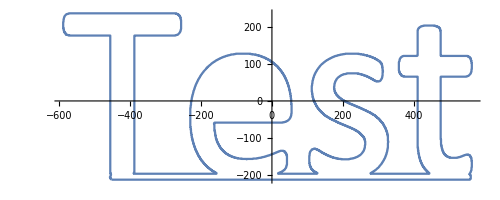

```mathematica
img=Import["C:\\Users\\Naught\\Downloads\\test.png"];
img=Binarize[img~ColorConvert~"Grayscale"~ImageResize~1200~Blur~0.1];
pts=DeleteDuplicates@Cases[Normal@ListContourPlot[Reverse@ImageData[img],Contours->{0.5}],_Line,-1][[1,1]];
center=Mean@MinMax[pts]&/@Transpose@pts;
pts=Map[{-Part[ImageDimensions[img],1]/2,-Part[ImageDimensions[img],2]/2}+#&,pts];;
GraphicsRow[{img,ListLinePlot[pts,AspectRatio->Full]}]
```

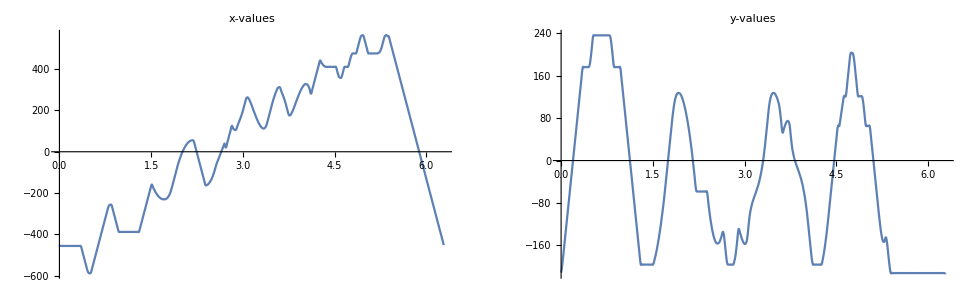

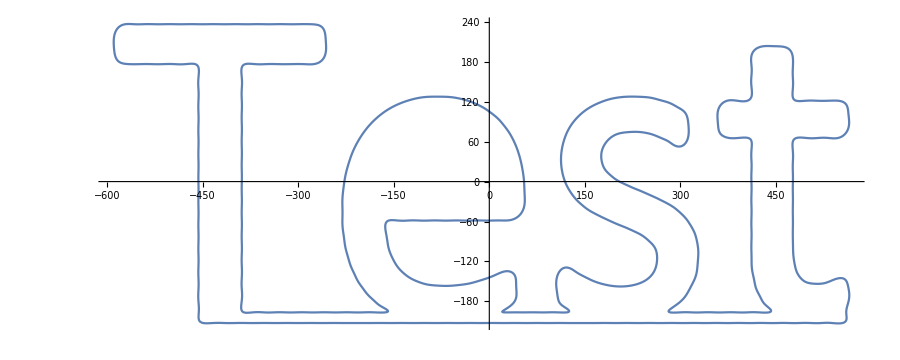

```mathematica
SetAttributes[toPt,Listable]
toPt[z_]:=ComplexExpand[{Re@z,Im@z}]//Chop;
cf=Compile[{{z,_Complex,1}},Module[{n=Length@z},1/n*Table[Sum[z[[k]]*Exp[-I*i*k*2 Pi/n],{k,1,n}],{i,-m,m}]]];
z=pts[[All,1]]+I*pts[[All,2]];
m = 200;
cn=cf[z];
{x[t_],y[t_]}=Sum[cn[[j]]*Exp[I*(j-m-1)*t],{j,1,2 m+1}]//toPt;
xmin = Part[Minimize[{x[t],0<t<2*Pi},t],1];
xmax = Part[Maximize[{x[t],0<t<2*Pi},t],1];
ymin = Part[Minimize[{y[t],0<t<2*Pi},t],1];
ymax = Part[Maximize[{y[t],0<t<2*Pi},t],1];
GraphicsRow[{Plot[x[t],{t,0,2*Pi},PlotLabel->"x-values",ImageSize->450],Plot[y[t],{t,0,2*Pi},PlotLabel->"y-values",ImageSize->450]}]
ParametricPlot[{x[t],y[t]},{t,0,2 Pi},AspectRatio->Automatic,ImageSize->900]
```

```mathematica
r=Abs/@cn;
theta=Arg/@cn;
index={m+1}~Join~Riffle[Range[m+2,2 m+1],Reverse[Range[1,m]]];
tPoints = Table[cn[[j]]*Exp[I*(j-m-1)*t],{j,index}]//toPt;
p[t_]=Accumulate@tPoints;
circles[t_]=Table[Circle[p[t][[i]],r[[index[[i]]]]],{i,1,2 m+1}];

anims=ParallelTable[ParametricPlot[{x[s],y[s]},{s,0,t},AspectRatio->Automatic,Epilog->{circles[t][[2;;]],Line[p[t]],Point[p[t]]},PlotRange->{{xmin,xmax},{ymin,ymax}},ImageSize->1200],{t,Subdivide[0.1,4 Pi,600]}];
```

$Aborted

```mathematica
For[i=1,i<601,i++1,Export[StringJoin["asc",ToString[i],".gif"],anims[[i]]]]
```

```mathematica
xmin
```

-589.539

```mathematica
ymin
```

-212.918